# Nutrient Limiting Regimes

```mathematica
ClearAll["Global`*"]
```

## Setup

```mathematica
colors={h->ColorData[97][2],s->ColorData[97][1]}; 
red=ResourceFunction["HexToColor"]["#FF1F5b"];
green=ResourceFunction["HexToColor"]["#00CD6C"];
blue = ResourceFunction["HexToColor"]["#009ADE"];
purple=ResourceFunction["HexToColor"]["#AF58BA"];
yellow=ResourceFunction["HexToColor"]["#FFC61E"];
orange=ResourceFunction["HexToColor"]["F28522"];
bestfit={aX->0.07243165880437435,wX->0.0026142991079086157,pX->27.700459925037663,ynX->0.060192963245436854,dsX->0.7709975010970849,dhX->0.12619563820188512,h0X->6.502940605096842*^-6,s0X->1.0227841615913929*^-10,rcX->0.009992087726261166,rnX->0.014645292219590888};(*paraeter fits in X format*)
fipar={a->0.07243165880437435,w->0.0026142991079086157,p->27.700459925037663,yn->0.060192963245436854,ds->0.7709975010970849,dh->0.12619563820188512,rc->0.009992087726261166,rn->0.014645292219590888};(*parameter fits without X format*)
parsFixed={nnh->0.18,nns->0.13};(*fixed parameter alues*)
```

## Model

```mathematica
tmax=8; (* 8-week time set *)
sim[pars_]:=Module[{jsc,jsn,jhc,jhn,jsg,jst,jhg,jht,f},(*Simulation*)
f=s[t](a h[t])/(s[t]+a w h[t]);(*equation 13*)
jsc=p s[t]; (*equation 6*)
jsn=yn nnh f; (*equation 5*)
jhc= p s[t]-Min[jsc,nns^-1 jsn]+rc h[t]^(2/3);(*equations 10 and 11*)
jhn=rn  h[t]^(2/3);(*equation 9*)
jsg=Min[jsc,nns^-1 jsn]; (*equation 3*)
jst=ds s[t]; (*equation 4*)
jhg=Min[jhc,nnh^-1 jhn];(*equation 7*)
jht=dh h[t] + f;(*equation 8*)
Quiet@NDSolve[
{
s'[t]==jsg-jst,(*equation 1*)
h'[t]==jhg-jht,(*equation 2*)
s[0]==s0,
h[0]==h0
}/.pars,
{s,h},
{t,0,tmax},Method->{Automatic,"DiscontinuityProcessing"->None},WorkingPrecision->20][[1]]];
pars[treatment_]:=(*parameter choices function*)Piecewise[{{Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->0,rn->0,s0->0,h0->h0X},parsFixed], treatment=="as"}, {Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->rcX,rn->rnX,s0->0,h0->h0X},parsFixed], treatment=="af"}, {Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->rcX,rn->rnX,s0->s0X,h0->h0X},parsFixed], treatment=="if"}, {Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->0,rn->0,s0->s0X,h0->h0X},parsFixed], treatment=="is"}}]
```

## Nutrient Limitations of Symbiont and Host

Here we explore where the Host and Symbiont are nitrogen or carbon limited depending for a given symbiont biomass (S) and host biomass (H).

```mathematica
(*Function that calculates limiting nutrients given an S and H*)
lim[x_,y_]:=Module[{jsc,jsn,jhc,jhn,jsg,jst,jhg,jht,f,ic},
ic={h0->y,s0->x};
f=s0(a h0)/(s0+a w h0);(*equation 13*)
jsc=p s0; (*equation 6*)
jsn=yn nnh f; (*equation 5*)
jhc= p s0-Min[jsc,nns^-1 jsn]+rc h0^(2/3);(*equations 10 and 11*)
jhn=rn  h0^(2/3);(*equation 9*)
jsg=Min[jsc,nns^-1 jsn]; (*equation 3*)
jst=ds s0; (*equation 4*)
jhg=Min[jhc,nnh^-1 jhn];(*equation 7*)
jht=dh h0 + f;(*equation 8*)
If[(jsc>jsn∧jhc>jhn)/.fipar/.ic/.parsFixed,1(*Print["SNHN"]*),
If[(jsc>jsn∧jhc<jhn)/.fipar/.ic/.parsFixed,2(*Print["SNHC"]*),
If[(jsc<jsn∧jhc<jhn)/.fipar/.ic/.parsFixed,3(*Print["SCHC"]*),4(*Print["SCHN"]*)]]]]
```

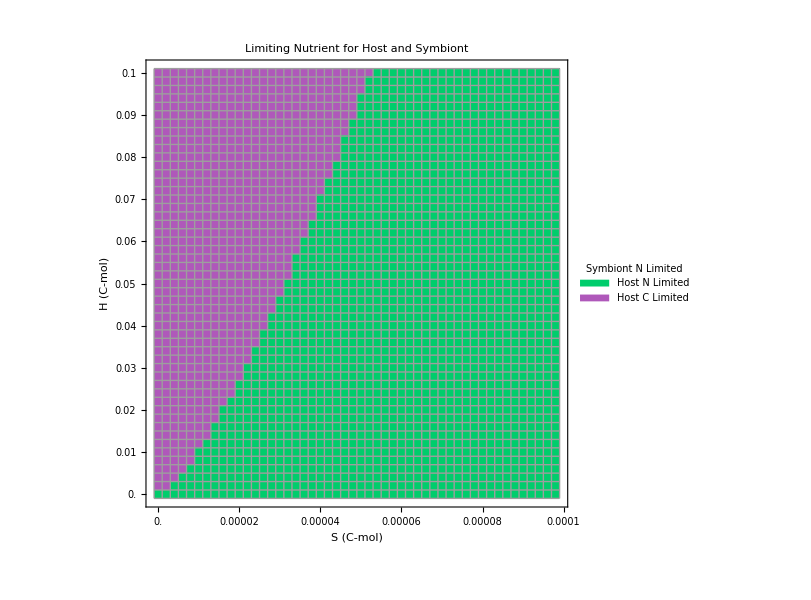

```mathematica
out2=Table[
Table[
lim[s,h],{s,10^-15,.0001,.000002}],{h,0,0.1,.002}];(*calculate nutrint liitation given an S and H*)
plotout2=ArrayPlot[Reverse[out2],AspectRatio->1,ColorRules->{1->green,2->purple,3->Green,4->Blue},Mesh->True,PlotLegends->SwatchLegend[{"Host N Limited","Host C Limited",SCHC,SCHN},LegendLabel->"Symbiont N Limited"],Frame->True,FrameLabel->{"H (C-mol)","S (C-mol)"},FrameTicks->{{Table[{51-(h)/2,h.001},{h,0,100,10}],None},{Table[{(s/2+1),.000001s},{s,0,100,20}],None}},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->20},ImageSize->600,PlotLabel->"Limiting Nutrient for Host and Symbiont"] (*plot Limiting nutrient*)
```

Here it is clear that the Symbiont is never carbon limited. This is an artifact of the model construction as the symbiont only shares leftover carbon with the host. Therefore the symbiont is only carbon limited. Furthermore this plot makes it clear that increasing symbiont biomass results is a shift from a carbon limited at low symbiont biomass to a nitrogen limited at a high symbiont biomass.

## Nutrient Limitation regimes when parameters are individually adjusted

Here we will explore the changes in nutrient limitation as a parameter changes, as seen in figure 4 and 5. In order to calculate δ we use the biomass from both the with symbiont fed scenario and the without symbiont fed scenario. To summarize the nutrient limitation fro a given parameter value we will take the integral of each nutrient through the simulation (8 weeks). This will show us the flux of each nutrients throughout the entire simulations for each organism and each scenario. We will then divide the integral of the carbon flux with the integral of the biomass adjusted nitrogen flux:
Host: ((∫_0)^8 j_ch(t)dt)/(nnh (∫_0)^8 j_nh(t)dt)
Symbiont: ((∫_0)^8 j_cs(t)dt)/(nns(∫_0)^8 j_ns(t)dt)
We will represent this fraction as (∫C)/(∫N). When (∫C)/(∫N) is greater than 1, the organism is generally carbon limited and when (∫C)/(∫N) is less than 1 the organism is generally nitrogen limited. We will then plot  (∫C)/(∫N) while varying a parameter value to explore shifts in general nutrient limitations and improve the understanding of the dynamics seen in figure 4 and 5.

```mathematica
jch[t_]:=h[t]^(2/3) rc+p s[t]-Min[p s[t],(a h[t] nnh s[t] yn)/(nns (s[t]+a h[t] w))](*host carbon*)
jnh[t_]:=h[t]^(2/3) rn(*host nitrogen*)
jcs[t_]:=p s[t](*symbiont carbon*)
jns[t_]:=(a h[t] nnh s[t] yn)/(s[t]+a h[t] w)(*symbiont nitrogen*)
(*Host: with symbiont, fed*)
dhoutif[varx_,var_,val_]:=Module[{sol},
sol=sim[pars["if"]/.varx->val/.bestfit]/.parsFixed;
(NIntegrate[jch[t]/.var->val/.sol/.parsFixed/.fipar,{t,0,8}]/(nnh NIntegrate[jnh[t]/.var->val/.sol/.parsFixed/.fipar,{t,0,8}]))/.parsFixed]
(*Host: without symbiont, fed*)
dhoutaf[varx_,var_,val_]:=Module[{sol},
sol=sim[pars["af"]/.varx->val/.bestfit]/.parsFixed;
(NIntegrate[jch[t]/.var->val/.sol/.parsFixed/.fipar,{t,0,8}]/(nnh NIntegrate[jnh[t]/.var->val/.sol/.parsFixed/.fipar,{t,0,8}]))/.parsFixed]
(*Symbiont: withsymbiont, fed*)
dsoutif[varx_,var_,val_]:=Module[{sol},
sol=sim[pars["if"]/.varx->val/.bestfit]/.parsFixed;
(NIntegrate[jcs[t]/.var->val/.sol/.parsFixed/.fipar,{t,0,8}]/(nns NIntegrate[jns[t]/.var->val/.sol/.parsFixed/.fipar,{t,0,8}]))/.parsFixed]
```

```mathematica
plotter[varx_,var_,rangea_,rangeb_]:=
GraphicsRow[{
LogPlot[
{dsoutif[varx,var,x],1},
{x,rangea,rangeb},
PlotStyle->{{s/.colors},{Black,Dashed}},
Frame->True,
FrameLabel->{{Rotate["(∫C)/(∫N)",3π/2],None},{var,None}},
LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->15},ImageSize->1000,RotateLabel->True],
LogPlot[{dhoutif[varx,var,x],
dhoutaf[varx,var,x],1},
{x,rangea,rangeb},
PlotStyle->{{h/.colors},{h/.colors,Dashed},{Black,Dashed}},
LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->15},
Frame->True,
FrameLabel->{{Rotate["(∫C)/(∫N)",3π/2],None},{var,None}},
ImageSize->1000]}]
```

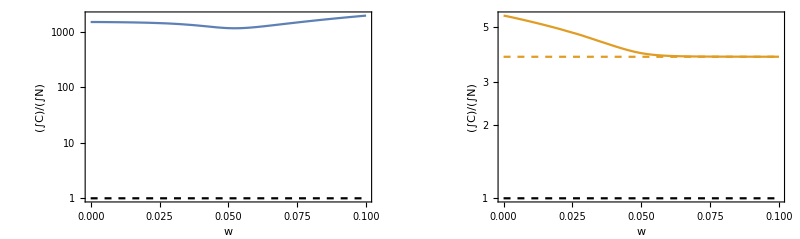

```mathematica
w2=plotter[wX,w,0,0.1]
```

-Graphics-

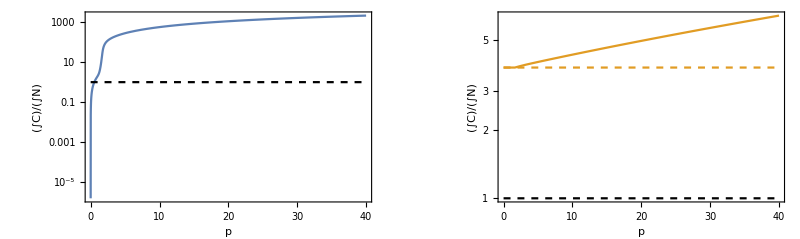

Mathematica has detected an internal error:
  iCopyExpr() called on symbol.

Please report this error as soon as possible to
support@wolfram.com giving as many details as possible
of the circumstances under which it occurred.

```mathematica
a2=plotter[aX,a,0,5];
w2=plotter[wX,w,0,0.1]
p2=plotter[pX,p,0,40]
yn2=plotter[ynX,yn,0,0.06]

ds2=plotter[dsX,ds,0,5]

dh2=plotter[dhX,dh,0,3]

rc2=plotter[rcX,rc,0,0.1]

rn2=plotter[rnX,rn,0,0.005]
```

These plots demonstrate that the symbiont and the host are generally carbon limited. It is important to note that changed in the value of the (∫C)/(∫N) represent general shifts between N limitation and C limitation within each 8 week simulation, even if over the host and symbiont appear universally carbon limited. As a result, these plots help show shifts in nutrient limitation resulting in changes in δ as a parameter value changes and seen in figure 4.

```mathematica
GraphicsColumn[{a2,w2,p2,yn2,ds2,dh2,rc2,rn2},ImageSize->1000]
```

-Graphics-

To better understand the dynamic seen in figure 5 we created the following 3 plots, representing (∫C)/(∫N) as p, the rate of photosynthesis and R, the feeding rate change.

```mathematica
(*adjust functions with only r and p as inputs*)
γ=bestfit[[10,2]]/bestfit[[9,2]];
dhoutif2[r_,p_]:=Module[{sol},
sol=sim[pars["if"]/.{rcX->r,rnX->γ r}/.pX->p/.bestfit]/.parsFixed;
(NIntegrate[jch[t]/.{rcX->r,rnX->γ r}/.pX->p/.sol/.parsFixed/.fipar,{t,0,8}]/(nnh NIntegrate[jnh[t]/.{rcX->r,rnX->γ r}/.pX->p/.sol/.parsFixed/.fipar,{t,0,8}]))/.parsFixed]
(*Host: without symbiont, fed*)
dhoutaf2[r_,p_]:=Module[{sol},
sol=sim[pars["af"]/.{rcX->r,rnX->γ r}/.pX->p/.bestfit]/.parsFixed;
(NIntegrate[jch[t]/.{rcX->r,rnX->γ r}/.pX->p/.sol/.parsFixed/.fipar,{t,0,8}]/(nnh NIntegrate[jnh[t]/.{rcX->r,rnX->γ r}/.pX->p/.sol/.parsFixed/.fipar,{t,0,8}]))/.parsFixed]
(*Symbiont: withsymbiont, fed*)
dsoutif2[r_,p_]:=Module[{sol},
sol=sim[pars["if"]/.{rcX->r,rnX->γ r}/.pX->p/.bestfit]/.parsFixed;
(NIntegrate[jcs[t]/.{rcX->r,rnX->γ r}/.pX->p/.sol/.parsFixed/.fipar,{t,0,8}]/(nns NIntegrate[jns[t]/.{rcX->r,rnX->γ r}/.pX->p/.sol/.parsFixed/.fipar,{t,0,8}]))/.parsFixed]
```

```mathematica
dhoutif2[1,1]
```

3.79041

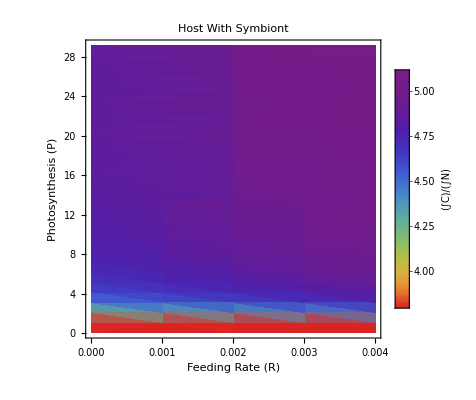

```mathematica
out1=Flatten[Table[
Table[
{r,p,dhoutif2[r,p]},{r,0,0.0045,0.001}],{p,0.1,30,1}],1];
test1=ListDensityPlot[
out1,
PlotRange->Full,
ColorFunction->(ColorData["Rainbow",(1-#)^2]&),
FrameLabel->{"Feeding Rate (R)","Photosynthesis (P)"},
LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->15},
PlotLabel->"Host With Symbiont",
PlotLegends->BarLegend[Automatic,LegendLabel->Style["(∫C)/(∫N)",FontFamily->"Times New Roman",FontColor->Black,FontSize-> 20]]]
```

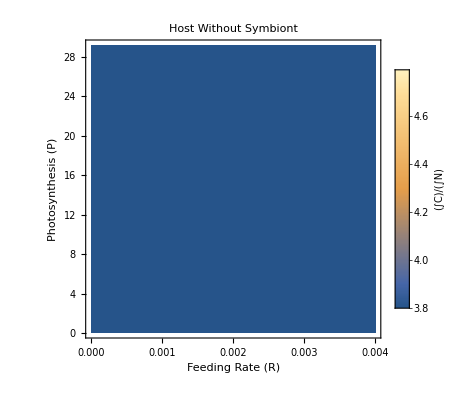

```mathematica
out3=Flatten[Table[
Table[
{r,p,dhoutaf2[r,p]},{r,0,0.0045,0.001}],{p,0.1,30,1}],1];

test3=ListDensityPlot[
out3,
PlotRange->All,
FrameLabel->{"Feeding Rate (R)","Photosynthesis (P)"},
LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->15}, 
 PlotLabel->"Host Without Symbiont",
PlotLegends->BarLegend[Automatic,LegendLabel->Style["(∫C)/(∫N)",FontFamily->"Times New Roman",FontColor->Black,FontSize-> 20]]]
```

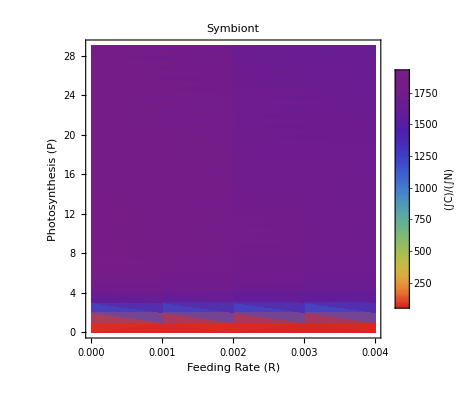

```mathematica
out2=Flatten[Table[
Table[
{r,p,dsoutif2[r,p]},{r,0,0.0045,0.001}],{p,0.0000000001,30,1}],1];
test2=ListDensityPlot[out2,PlotRange->All,ColorFunction->(ColorData["Rainbow",(1-#)^2]&),PlotLabel->"Symbiont",
LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->15},
FrameLabel->{"Feeding Rate (R)","Photosynthesis (P)"},
PlotLegends->BarLegend[Automatic,LegendLabel->Style["(∫C)/(∫N)",FontFamily->"Times New Roman",FontColor->Black,FontSize-> 20]]]
```